```mathematica
ClearAll[Ω]
chi=1;
Ω=10;
```

```mathematica
(*Probability of atom in upper or Lower State based on Optical Bloch Equation Solutions*)

P2[t_]:=1/2(chi/Ω)^2*(1-N[Cos[Ω*t]])
```

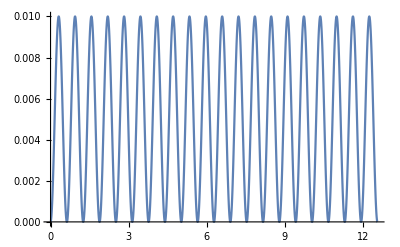

```mathematica
Plot[P2[t],{t,0,4π}]
```